```mathematica
RandomGraph[WattsStrogatzGraphDistribution[50,0.1,50]]
```

-Graphics-

-Graphics-

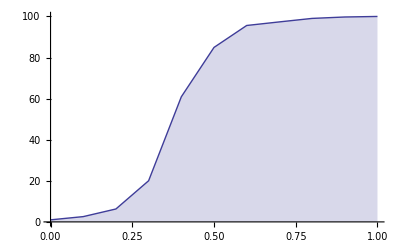

```mathematica
network=RandomGraph[WattsStrogatzGraphDistribution[100,0.1,3]];
infect[z_,p_]:=Pick[z,RandomChoice[{p,1-p}->{1,0},Length[z]],1];
step[g_,{i_,q_},p_]:=
{Complement[infect[AdjacencyList[g,i],p],i,q],Join[q,i]};
infected[g_,i_,p_]:=Last[FixedPoint[step[g,#,p]&,{i,{}}]]
infected{network,{1},0.4}//short;
HighlightGraph[network,%]
count[p_]:=Mean[Table[Length[infected[network,{1},p]],{100}]];
DiscretePlot[count[p],{p,0,1,0.1},Joined-> True]
```